```mathematica
AbsoluteTiming[Get[FileNameJoin[{NotebookDirectory[],"FunctionDefinitions.wl"}]]]
ClearAll[SyncDownValues];
SetAttributes[SyncDownValues,HoldAll];
SyncDownValues[M_Symbol]:=(DownValues[M]={DownValues[M],ParallelEvaluate[DownValues[M],DistributedContexts->None]}//Association//Normal;);
```

{28.9754,Null}

## Constructing a cache of results

### SDP Results

```mathematica
ClearAll[CachedSDPResult];
SetAttributes[CachedSDPResult,HoldAll];
CachedSDPResult[rhoIn_,rhoFin_,t_?(VectorQ[#,NumericQ]&),HoldPattern[Hamiltonian[ω_,Δω_,DiagonalMatrix[{XX_?NumericQ,YY_?NumericQ,ZZ_}]]]]:=
CachedSDPResult[rhoIn,rhoFin,t,Hamiltonian[ω,Δω,DiagonalMatrix[{XX,YY,ZZ}]]]=SDPResult[rhoIn,rhoFin,Evaluate[N[t]],Hamiltonian[ω,Δω,DiagonalMatrix[{XX,YY,ZZ}]]];
CausalityConstraints[3];
```

#### Detuned initial state |0><0|

```mathematica
With[
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,1}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5/Δω,
plottingRange=Range@@{0,1,10^-3}
},
{fun=γ|->CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]]},
ParallelMap[fun,plottingRange];
SyncDownValues[CachedSDPResult];
]
```

SemidefiniteOptimization::noprog: Lack of progress.

SemidefiniteOptimization::dfedge: Stuck at edge of dual feasibility.

#### Dimensionless detuning

```mathematica
With[
{
ω=1000,
JPerp=1,
Jz=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,1}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=π/(3*2*JPerp),
plottingRange=PowerRange[10^-2,100,30/29]
},
{fun=δ|->CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω/2,JPerp δ,DiagonalMatrix[{JPerp/2,JPerp/2,Jz}]]]},
ParallelMap[fun,plottingRange];
SyncDownValues[CachedSDPResult];
]
```

#### Detuned initial state |+><+|

```mathematica
With[
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{1,0,0}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5Δω,
plottingRange=Range@@{0,1,10^-3}
},
{fun=γ|->CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]]},
ParallelMap[fun,plottingRange];
SyncDownValues[CachedSDPResult];
]
```

#### Detuned initial state |+><+| against ZZ coupling

```mathematica
With[
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{1,0,0}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5Δω
},
{fun={γ,z}|->SDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Evaluate[N[Δω]],DiagonalMatrix[{γ Δω,γ Δω,z Δω}]]]["Population"]},
KeyValueMap[
With[{γ=#1[[1]],z=#1[[2]],res=#2},
CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,z Δω}]]]=<|"Population"->res|>
]&,ParallelDensityPlotData[fun,{γ,0,1},{z,0,1},"MaxIters"->4]];
]
```

#### Detuned initial state (1-ϵ) |0><0| + ϵ |1><1| (rhoQubit[{0,0,1-2ϵ}])

```mathematica
With[
{ϵ=3/10},
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,1-2ϵ}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5Δω,
plottingRange=Range@@{0,1,10^-3}
},
{fun=γ|->CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]]},
ParallelMap[fun,plottingRange];
SyncDownValues[CachedSDPResult];
]
```

#### Dimensionless detuning

```mathematica
With[
{
ω=1000,
JPerp=1,
Jz=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,4/5}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=π/(2*2*JPerp),
plottingRange=PowerRange[10^-2,100,30/29]
},
{fun=δ|->CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω/2,JPerp δ,DiagonalMatrix[{JPerp/2,JPerp/2,Jz}]]]},
ParallelMap[fun,plottingRange];
SyncDownValues[CachedSDPResult];
]
```

### Optimizing over unitaries

```mathematica
SetAttributes[CachedUnitaryStrategy,HoldAll];
CachedUnitaryStrategy[rhoIn_,rhoFin_,t_,HoldPattern[Hamiltonian[ω_,Δω_,DiagonalMatrix[{XX_?NumericQ,YY_?NumericQ,ZZ_}]]]]:=CachedUnitaryStrategy[rhoIn,rhoFin,t,Hamiltonian[ω,Δω,DiagonalMatrix[{XX,YY,ZZ}]]]=UnitaryStrategy[rhoIn,rhoFin,Evaluate[N[t]],Hamiltonian[ω,Δω,DiagonalMatrix[{XX,YY,ZZ}]]];
```

#### Detuned initial state |0><0|

```mathematica
With[
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,1}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5Δω,
plottingRange=Range@@{0,1,10^-3}
},
{fun=γ|->CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]]},
ParallelMap[fun,plottingRange];
SyncDownValues[CachedUnitaryStrategy];
]
```

#### Dimensionless detuning

```mathematica
With[
{
ω=1000,
JPerp=1,
Jz=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,1}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=π/(3*2*JPerp),
plottingRange=PowerRange[10^-2,100,30/29]
},
{fun=δ|->CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω/2,JPerp δ,DiagonalMatrix[{JPerp/2,JPerp/2,Jz}]]]},
ParallelMap[fun,plottingRange];
SyncDownValues[CachedUnitaryStrategy];
]
```

#### Detuned initial state |+><+|

```mathematica
With[
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{1,0,0}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5Δω,
plottingRange=Range@@{0,1,10^-3}
},
{fun=γ|->CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]]},
ParallelMap[fun,plottingRange];
SyncDownValues[CachedUnitaryStrategy];
]
```

#### Detuned initial state |+><+| against ZZ coupling

```mathematica
With[
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{1,0,0}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5Δω
},
{fun={γ,z}|->UnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Evaluate[N[Δω]],DiagonalMatrix[{γ Δω,γ Δω,z Δω}]]]["Population"]},
KeyValueMap[
With[{γ=#1[[1]],z=#1[[2]],res=#2},
CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,z Δω}]]]=<|"Population"->res|>
]&,ParallelDensityPlotData[fun,{γ,0,1},{z,0,1},"MaxIters"->4]];
]
```

$Aborted

#### Detuned initial state (1-ϵ) |0><0| + ϵ |1><1| (rhoQubit[{0,0,1-2ϵ}])

```mathematica
With[
{ϵ=3/10},
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,1-2ϵ}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5Δω,
plottingRange=Range@@{0,1,10^-3}
},
{fun=γ|->CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]]},
ParallelMap[fun,plottingRange];
SyncDownValues[CachedUnitaryStrategy];
]
```

#### Dimensionless detuning

```mathematica
With[
{
ω=1000,
JPerp=1,
Jz=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,4/5}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=π/(2*2*JPerp),
plottingRange=PowerRange[10^-2,100,30/29]
},
{fun=δ|->CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω/2,JPerp δ,DiagonalMatrix[{JPerp/2,JPerp/2,Jz}]]]},
ParallelEvaluate[SetOptions[UnitaryStrategy,Method->{"NelderMead", "ShrinkRatio"->0.65,"ContractRatio"->0.65,"ReflectRatio"->1.25,"RandomSeed"->2}]];
ParallelMap[fun,plottingRange];
SyncDownValues[CachedUnitaryStrategy];
ParallelEvaluate[SetOptions[UnitaryStrategy,Method->Automatic]];
]
```

### Optimizing over Markovian channels

```mathematica
SetAttributes[CachedSeeSawMarkovian,HoldAll];
CachedSeeSawMarkovian[rhoIn_,rhoFin_,t_?(VectorQ[#,NumericQ]&),HoldPattern[Hamiltonian[ω_,Δω_,DiagonalMatrix[{XX_?NumericQ,YY_?NumericQ,ZZ_}]]]]:=
CachedSeeSawMarkovian[rhoIn,rhoFin,t,Hamiltonian[ω,Δω,DiagonalMatrix[{XX,YY,ZZ}]]]=SeeSawMarkovian[rhoIn,rhoFin,Evaluate[N[t]],Hamiltonian[ω,Δω,DiagonalMatrix[{XX,YY,ZZ}]]];
```

#### Detuned initial state (1-ϵ) |0><0| + ϵ |1><1| (ρQubit[{0,0,4/5}])

```mathematica
With[
{ϵ=3/10},
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,1-2ϵ}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5Δω,
plottingRange=Range@@{0,1,10^-3}
},
{fun=γ|->CachedSeeSawMarkovian[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]]},
ParallelMap[fun,plottingRange];
SyncDownValues[CachedSeeSawMarkovian];
]
```

#### Dimensionless detuning

```mathematica
With[
{
ω=1000,
JPerp=1,
Jz=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,4/5}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=π/(2*2*JPerp),
plottingRange=PowerRange[10^-2,100,30/29]
},
{fun=δ|->CachedSeeSawMarkovian[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω/2,JPerp δ,DiagonalMatrix[{JPerp/2,JPerp/2,Jz}]]]},
ParallelMap[fun,plottingRange];
SyncDownValues[CachedSeeSawMarkovian];
]
```

## Plots

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/simon/IndirectControl

```mathematica
Needs["MaTeX`"]
MaTeX["x^2"]
```

-Graphics-

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,bm}"},FontSize->14]
MaTeX["\\matrixel{1}{a^\\dag}{0}_\\beta=1"]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{physics,bm}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→14,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

-Graphics-

```mathematica
StyledPlot[data_]:=ListLinePlot[
data,
PlotTheme->{"Academic","DashedLines"},
PlotRange->{.45,1.05},
PlotMarkers->None,
PlotStyle->{{AbsoluteThickness[2],Opacity[1]},{AbsoluteThickness[3],Opacity[.6]}},
FrameLabel->{ MaTeX["g_\\perp"],MaTeX["\\matrixel{0}{\\rho_{out}}{0}"]},
GridLines->Automatic,
GridLinesStyle->LightGray,
ImageSize->320
];
```

```mathematica
StyledLogPlot[data_,opt:OptionsPattern[ListLinePlot]]:=ListLogLinearPlot[
data,
opt,
Joined->True,
PlotMarkers->None,
PlotTheme->{"Scientific","DashedLines","VibrantColor"},
PlotRange->{{10^-2,10^2},{.45,1.05}},
PlotStyle->{{AbsoluteThickness[2],Opacity[1]},{AbsoluteThickness[3],Opacity[.6]}},
FrameStyle->Directive[Black,AbsoluteThickness[1],FontSize->12],
TicksStyle->Directive[Black,FontSize->12],
FrameTicksStyle->Directive[FontSize->12],
FrameLabel->{ MaTeX["\\delta"],MaTeX["\\matrixel{0}{\\rho_{out}}{0}"]},
GridLines->Automatic,
GridLinesStyle->LightGray,
ImageSize->320
]
```

### fig:OptimalVsUnitaryZeroState

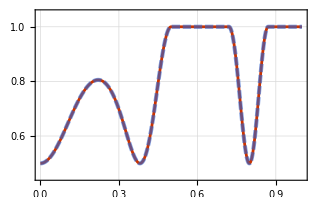

```mathematica
With[
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,1}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5Δω,
plottingRange={γ,0,1,10^-3}
},
{
fun1=γ|->CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]],
fun2=γ|->CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]]
},
StyledPlot[{
Table[{γ,fun1[γ]["Population"]},plottingRange],Table[{γ,fun2[γ]["Population"]},plottingRange]
}]
]
```

```mathematica
Export["Figures/Plots/OptimalVsUnitaryZeroState.png",,ImageResolution->600]
```

Figures/Plots/OptimalVsUnitaryZeroState.png

#### Dimensionless detuning

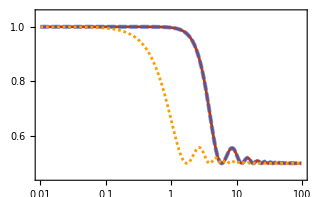

```mathematica
With[
{
ω=1000,
JPerp=1,
Jz=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,1}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=π/(3*2*JPerp),
plottingRange={δ,PowerRange[10^-2,100,30/29]}
},
{
fun1=δ|->CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω/2,JPerp δ,DiagonalMatrix[{JPerp/2,JPerp/2,Jz}]]],
fun2=δ|->CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω/2,JPerp δ,DiagonalMatrix[{JPerp/2,JPerp/2,Jz}]]]
},
StyledLogPlot[{
Table[{δ,fun1[δ]["Population"]},plottingRange],Table[{δ,fun2[δ]["Population"]},plottingRange],Table[{δ,1/2(1+(Sin[JPerp*3t*Sqrt[1+δ^2]]^2)/(1+δ^2))},plottingRange]
}]
]
```

### fig:OptimalVsUnitaryPlusState

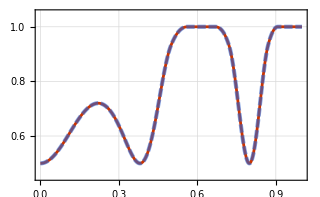

```mathematica
With[
{
ω=1000,
Δω=1,
rhoFin=rhoQubit[{0,0,1}],
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{1,0,0}]
},
{
t=5Δω,
plottingRange={γ,0,1,10^-3}
},
{fun1=γ|->CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]],
fun2=γ|->CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]]
},
StyledPlot[{
Table[{γ,fun1[γ]["Population"]},plottingRange],Table[{γ,fun2[γ]["Population"]},plottingRange]
}]
]
```

```mathematica
Export["Figures/Plots/OptimalVsUnitaryPlusState.png",]
```

Figures/Plots/OptimalVsUnitaryPlusState.png

#### Detuned initial state |+><+| against ZZ coupling

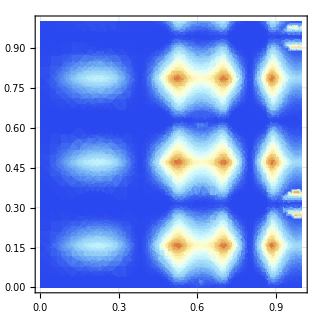

```mathematica
With[
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{1,0,0}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5Δω
},
{
contours=Range[0,1,.05]
},
{
fun1={γ,z}|->CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,z Δω}]]]["Population"],
fun2={γ,z}|->CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,z Δω}]]]["Population"]
},
ParallelDensityPlotData[Abs[fun2[##]-fun1[##]]&,{γ,0,1},{z,0,1},"MaxIters"->4]//ListDensityPlot[#,

]&
]
```

```mathematica
Export["Figures/Plots/OptimalVsUnitaryPlusState.png",,ImageResolution->600]
```

Figures/Plots/OptimalVsUnitaryPlusState.png

### fig:OptimalVsUnitaryMixed

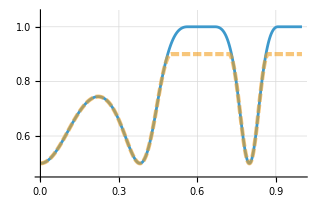

```mathematica
With[
{ϵ=1/10},
{
ω=1000,
Δω=1,
rhoFin=rhoQubit[{0,0,1}],
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,1-2ϵ}]
},
{
t=5Δω,
plottingRange={γ,0,1,10^-3}
},
{fun1=γ|->CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]],
fun2=γ|->CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]]
},
StyledPlot[{
Table[{γ,fun1[γ]["Population"]},plottingRange],Table[{γ,fun2[γ]["Population"]},plottingRange]
}]
]
```

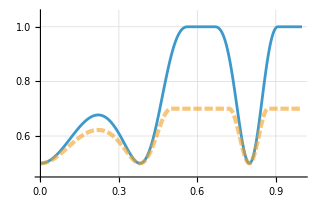

```mathematica
Export["Figures/Plots/OptimalVsUnitaryMixed.png",,ImageResolution->600]
```

Figures/Plots/OptimalVsUnitaryMixed.png

#### Dimensionless detuning

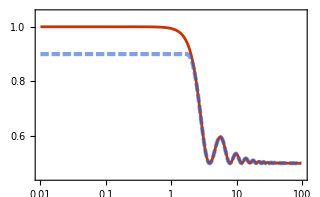

```mathematica
With[
{
ω=1000,
JPerp=1,
Jz=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,4/5}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=π/(2*2*JPerp),
plottingRange={δ,PowerRange[10^-2,100,30/29]}
},
{
fun1=δ|->CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω/2,JPerp δ,DiagonalMatrix[{JPerp/2,JPerp/2,Jz}]]],
fun2=δ|->CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω/2,JPerp δ,DiagonalMatrix[{JPerp/2,JPerp/2,Jz}]]]
},
StyledLogPlot[{
Table[{δ,fun1[δ]["Population"]},plottingRange],Table[{δ,fun2[δ]["Population"]},plottingRange]
}]
]
```

### fig : HeuristicComparison

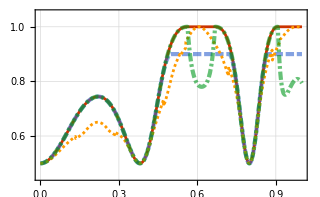

```mathematica
With[
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,4/5}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5Δω,
plottingRange={γ,0,1,10^-3}
},
{
SDP=γ|->CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]],
MARK=γ|->CachedSeeSawMarkovian[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]]["Population"],
UNIT=γ|->CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]]["Population"]
},
{
ReducedSDP=γ|->Re@Tr[Transpose[ProcessCombMatrix[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0.}]]]].((mat|->1/4KroneckerProduct[MatrixPartialTrace[mat,3;;4,2],MatrixPartialTrace[mat,1;;2,2]])[SDP[γ]["Tester"]])]
},
StyledPlot[
{
Table[{γ,SDP[γ]["Population"]},plottingRange],
Table[{γ,UNIT[γ]},plottingRange],
Table[{γ,MARK[γ]},plottingRange],
Table[{γ,ReducedSDP[γ]},plottingRange]
}
]
]
```

```mathematica
Export["Figures/Plots/HeuristicsComparisonMixedState.png",,ImageResolution->600]
```

Figures/Plots/HeuristicsComparisonMixedState.png

#### Dimensionless detuning

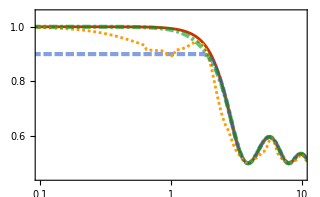

```mathematica
With[
{
ω=1000,
JPerp=1,
Jz=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,4/5}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=π/(2*2*JPerp),
plottingRange={δ,PowerRange[10^-2,100,30/29]}
},
{
SDP=δ|->CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω/2,JPerp δ,DiagonalMatrix[{JPerp/2,JPerp/2,Jz}]]],
MARK=δ|->CachedSeeSawMarkovian[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω/2,JPerp δ,DiagonalMatrix[{JPerp/2,JPerp/2,Jz}]]]["Population"],
UNIT=δ|->CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω/2,JPerp δ,DiagonalMatrix[{JPerp/2,JPerp/2,Jz}]]]["Population"]
},
{
ReducedSDP=δ|->Re@Tr[Transpose[ProcessCombMatrix[rhoIn,rhoFin,Evaluate[N[{t,t,t}]],Hamiltonian[ω/2,JPerp δ,DiagonalMatrix[{JPerp/2,JPerp/2,Jz}]]]].((mat|->1/4KroneckerProduct[MatrixPartialTrace[mat,3;;4,2],MatrixPartialTrace[mat,1;;2,2]])[SDP[δ]["Tester"]])]
},
StyledLogPlot[
{
Table[{δ,SDP[δ]["Population"]},plottingRange],
Table[{δ,UNIT[δ]},plottingRange],
Table[{δ,MARK[δ]},plottingRange],
Table[{δ,ReducedSDP[δ]},plottingRange]
},
PlotRange->{{10^-1,10^1},{.45,1.05}}
]
]
```